# Mappa logistica

Cammelli Tonanti, ovvero Riccardo Cazzin e Francesco Tognetti

Università degli Studi di Padova

Le iterazioni della mappa logistica f_μ=μx(1-x), che dipende dal parametro positivo μ, costituiscono (a prima vista) una versione discreta della dinamica continua descritta dall’equazione logistica. A differenza di quest’ultima, però, la dinamica discreta della mappa logistica è enormemente complicata.

## Lemmi introduttivi e visualizzazione delle orbite.

Con mappa logistica intendiamo la funzione polinomiale reale f_μ(x)=μ x (1-x), con μ>0. Ci occuperemo soprattutto delle iterazioni di f_μ, ossia delle funzioni f_μ^n=f_μ∘…∘f_μ: studieremo, al variare del parametro μ, il comportamento delle orbite generate da f_μ, ovvero degli insiemi del tipo {x_0,f_μ(x_0),f_μ^2(x_0),…}; in particolare, vedremo sotto quali ipotesi tali orbite posseggano uno o più attrattori. In seguito, mostreremo un’applicazione, resasi assai attuale nell’ultimo periodo, che modellizza l’andamento di un’epidemia proprio con la mappa f_μ.

```mathematica
(*Evitiamo di entrare in conflitto con altri progetti aperti.*)
ClearAll["Global`*"] 

(*Definiamo Subscript[f, μ]. Definiamo subito anche l'iterata di Subscript[f, μ], dato che la useremo molto spesso. Per risparmiare sui tempi di computazione conviene compilare fn e fnlist*)
f[μ_,x_]:=μ x(1-x)
fn=Compile[{{μ,_Real},{x,_Real},{n,_Integer}},Nest[μ#(1-#)&,x,n]] 
fnlist=Compile[{{μ,_Real},{x,_Real},{n,_Integer}},NestList[μ#(1-#)&,x,n]]
```

CompiledFunction[…]

CompiledFunction[…]

```mathematica
With[{fn[μ_,x_,n_]:=Nest[f[μ,#]&,x,n],fnC=Compile[{{μ,_Real},{x,_Real},{n,_Integer}},Nest[μ#(1-#)&,x,n]],test=First/@{fn[3.5,0.4,10^7];//Timing,fnC[3.5,0.4,10^7];//Timing}},(First[test]-Last[test])/First[test]]
```

Applicando in modo iterato la mappa logistica a partire da un punto iniziale x_0∈ℝ, ci chiediamo se la mappa ammetta un punto fisso, ovvero un x_f_μ∈ℝ tale che f_μ(x_f_μ)=x_f_μ.

Lemma 1. Per ogni μ>0, f_μ ha come unici punti fissi 0 e 1-1/μ.

Dimostrazione. Si può lasciare a Mathematica la soluzione dell’equazione di punto fisso: si applica First per rimuovere le espressioni condizionali, dato che il caso μ=1 dà come unico punto fisso con molteplicità doppia il punto x=0. I punti trovati sono quelli richiesti dal Lemma.

```mathematica
First/@(x/.Solve[{μ>0,f[μ,x]==x},x,Reals])
```

□

A priori la mappa logistica potrebbe essere studiata su tutto ℝ. Coi prossimi lemmi, invece, mostriamo che lo studio più fecondo avviene nell’intervallo [0,1].

Lemma 2. Per ogni μ>1, se x_0>1 oppure x_0<0, allora f_μ^n(x_0)→-∞.

Dimostrazione. Mostriamo innanzitutto per quali x∈ℝ si abbia f_μ(x)<x. Se risulta che, chiamato U il sottoinsieme di ℝ che verifichi la disuguaglianza sopra, a tale U appartengono sia f_μ(x_0) sia x_0 per ogni x_0>1 e per ogni x_0<0, allora f_μ^n(x_0) è una successione monotona decrescente inferiormente illimitata, e si è provata la tesi.

```mathematica
Reduce[{μ>1,f[μ,x]<x},x,Reals]
```

È evidente, poi, che f_μ(x_0)<0 per ogni x_0>1>1-1/μ e per ogni x_0<0, dunque la successione f_μ^n(x_0) diverge a -∞ in questi due casi.

□

Lemma 3. Se x_0<0 oppure x_0>1, allora esiste 0<μ≤1 tale che f_μ^n(x_0)→-∞.

Dimostrazione. Usiamo un approccio analogo a quello del Lemma 2:

```mathematica
Reduce[{0<μ≤1,f[μ,x]<x},x,Reals]
```

Trattiamo innanzitutto il caso x_0>1:

```mathematica
Reduce[{0<μ≤1,x0>1,f[μ,x0]<(-1+μ)/μ},x0,Reals]
```

Scegliendo 1>μ>1/x_0>0 si ottiene quanto richiesto. Trattiamo ora il caso x_0<0: poiché è sufficiente che x_0<1-1/μ, basta scegliere 1>μ>1/(1-x_0)>0.

□

Col prossimo lemma, infine, restringiamo l’intervallo dei μ che intendiamo prendere in considerazione.

Lemma 4. Se 0<μ≤4, allora tutte le orbite con dato iniziale in [0,1] rimangono in tale intervallo. Se, invece, μ>4, allora esiste un intervallo A_0⊆[0,1] tale che ogni orbita con dato iniziale in A_0 non è contenuta in [0,1] a partire dalla prima iterazione.

Dimostrazione. La prova del Lemma 4 è immediata, se si considerano le seguenti disuguaglianze:

```mathematica
Reduce[{0≤x≤1,0≤f[μ,x]≤1,0<μ≤4},x]
Reduce[{0≤x≤1,0≤f[μ,x]≤1,μ>4},x]
```

□

Alla luce di questo risultato, decidiamo di studiare la dinamica della mappa logistica per μ<4.

Dopo aver delimitato quanto più possibile gli intervalli da studiare, osserviamo come può evolvere un'orbita al variare di μ e x_0.

```mathematica
graficoOrbita[μ_,x_,n_]:=With[
{
(*Precalcoliamo l'orbita, disposta sulla bisettrice.*)
pts=Table[{ξ,ξ},{ξ,fnList[μ,x,n]}]
},
(*Disegniamo la parabola Subscript[f, μ] e la bisettrice del I e del III quadrante; mostriamo poi l'orbita tenendo traccia dell'ultimo punto (in azzurro).*)
Plot[
{f[μ,t],t},
{t,Min[x,0],Max[x,1]},

]]
```

```mathematica
Manipulate[graficoOrbita[μ,x0,n],{{μ,1.2},0,4},{{x0,0.4},0,1},{{n,21},Range[1,201,10]}]
```

## Biforcazioni e caos

Grazie al grafico dinamico sopra, si può notare che per 0<μ≤1 tutte le orbite tendono a 0, unico punto fisso in [0,1] per tali μ. Ciò è dovuto al fatto che, con 0<μ≤1, si ha f_μ(x)≤x per ogni x∈[0,1], ma al contempo f_μ(x)≥0 per tali x in base al Lemma 4: per il teorema sul limite di successioni monotone, qualunque orbita con dato iniziale in [0,1] ammette limite e tale limite è proprio 0. La situazione cambia se μ>1.

Lemma 5. Per ogni μ>1 il punto 0 è un punto fisso repulsivo di f_μ.

Dimostrazione. Un punto fisso x_0 è repulsivo per f_μ se e solo se |f'_μ(x_0)|>1. Dal momento che f'_μ(0)=μ>1, la tesi è verificata.

```mathematica
D[f[μ,x],x]/.x->0
```

□

Per μ>1 il punto fisso x_μ=1-1/μ appartiene a [0,1] e, dunque, può essere preso in considerazione.

Lemma 6.  Il punto fisso x_μ=1-1/μ per f_μ è attrattivo per 1<μ<3 e repulsivo per μ>3.

Dimostrazione. Con un ragionamento simile a quello usato nel Lemma 5, calcoliamo la derivata di f_μ in x_μ:

```mathematica
Simplify[D[f[μ,x],x]/.x->1-1/μ]
```

Dato che |2-μ|<1 per 1<μ<3 e |2-μ|>1 per μ>3, si è provata la tesi.

□

Nel caso 1<μ≤3, dunque, le orbite di tutti gli x∈(0,1) convergono a x_μ e le orbite di 0 e 1 convergono a 0. Come si può notare a livello grafico, però, la convergenza verso x_μ diviene sempre più lenta man mano che μ si avvicina a 3 e, superatolo, essa scompare per lasciare il posto ad orbite di periodo 2.

Lemma 7. L’orbita di periodo minimo 2 di f_μ esiste per μ>3 ed è attrattiva per 3<μ<1+√6.

Dimostrazione. Se un’orbita per f_μ ha come periodo minimo 2, allora i due punti attrattivi x_1 e x_2 sono punti fissi di f_μ^2. Calcoliamo, dunque, i punti fissi di f_μ^2

```mathematica
Solve[{fn[μ,x,2]==x,μ>0,0≤x≤1},x,Reals]
```

Confrontando i quattro risultati ottenuti con i punti fissi di f_μ, spostiamo l’attenzione sugli ultimi due risultati, che valgono per μ>3. Calcoliamo la derivata di f_μ^2 nei punti fissi appena trovati:

```mathematica
Expand@FullSimplify[D[fn[μ,x,2],x]/.(Solve[{fn[μ,x,2]==x,μ>3},x,Reals]⟦{3,4}⟧/.ConditionalExpression[ξ_,_]->ξ)]
```

e vediamo per quali μ>3 sono punti attrattivi.

```mathematica
Reduce[RealAbs[#]<1&&μ>3,μ,Reals]&/@Expand@FullSimplify[D[fn[μ,x,2],x]/.(Solve[{fn[μ,x,2]==x,μ>3},x,Reals]⟦{3,4}⟧/.ConditionalExpression[ξ_,_]->ξ)]
```

Ciò conferma quanto affermato nella tesi.

□

Ogni nuova biforcazione è prodotta dallo stesso fenomeno analitico. Alla n-esima biforcazione, infatti, le orbite attrattive convergono ai punti fissi di f_μ^(2^n) che abbiano modulo della derivata strettamente minore di 1: posseggono questa caratteristica i punti fissi di f_μ^(2^n) che non sono anche punti fissi di f_μ^(2^(n-1)). Tali punti attrattivi compaiono non appena i punti fissi di f_μ^(2^n) che sono anche punti fissi di f_μ^(2^(n-1)) hanno derivata di modulo maggiore di 1; come si vede nel grafico sotto, infatti, la comparsa di nuovi attrattori è strettamente collegata al superamento della soglia 1 per il modulo della derivata calcolata negli attrattori “precedenti” — e questa crescita del modulo della derivata si ottiene con l’aumentare di μ.

```mathematica
Manipulate[
GraphicsRow[
{
Plot[{fn[μ,x,n],x},{x,0,1},
,
Epilog->{Red,Point[{x,x}]/.Solve[{fn[Rationalize@μ,x,n]==x,x≥0},x,Reals]}
],
Plot[{Abs[D[fn[μ,y,n],y]]/.y->x,1},{x,0,1},
,
Epilog->{Red,Point[{x,Abs[D[fn[μ,y,n],y]/.y->x]}]/.Solve[{fn[Rationalize@μ,x,n]==x,x≥0},x,Reals]}
]
}
],
{μ,3,3.57},
{n,2^Range[3]}
]
```

Dopo aver capito il motivo per il quale i punti perdono di attrattività dopo aver passato un certo μ, si può tracciare un grafico dei punti fissi e delle prime orbite attrattive al variare di μ: non vanno considerate in questo grafico le orbite non generate direttamente dalla biforcazione, perché di quelle non abbiamo dato spiegazione.

```mathematica
ListPlot[
Union@Flatten[
Table[
ParallelTable[{μ,x}/.NSolve[{fn[μ,x,n]==x,x≥0},x,Reals],{μ,Subdivide[0,4,10^4]}],
{n,2^Range[0,3]}
],
2
],

]
```

Questo grafico può essere “completato” registrando il comportamento dell’orbita di un singolo punto x_0 al variare di μ dopo un certo numero (alto) di iterazioni.

```mathematica
attrattivoData[n_,m_,{μ0_,μ1_,η_}]:=Union@Flatten[ParallelTable[,{μ,μ0,μ1,η}],1]
```

```mathematica
(*codaOrbita=attrattivoData[10^4,50,{0,4,10^-4}];*)(*Scegliamo di considerare al più le ultime 50 iterazioni calcolate per ogni μ*)
(*Se si vuole risparmiare tempo, è possibile importare codaOrbita già calcolato.*)
codaOrbita=Import["https://raw.githubusercontent.com/ZinRicky/cammelli-tonanti/master/01_Esame/03_Dati/C_completa.csv"];
```

```mathematica
Rasterize[ListPlot[codaOrbita,],ImageSize->1000]
```

Attraverso opportuni ingrandimenti, si nota che la struttura delle biforcazioni è in un certo senso autosimile: ogni nuova biforcazione mantiene una forma molto vicina alla precedente.

```mathematica
GraphicsGrid[Partition[MapThread[Rasterize[ListPlot[codaOrbita,],ImageSize->1000]&,],2],ImageSize->Full]
```

Quest’autosimilarità si ritrova non solo ad ogni biforcazione, ma anche nella parte di grafico in cui l’andamento delle orbite è meno regolare.

```mathematica
(*autoSimCaos=attrattivoData[10^4,100,{3.56,4,2 10^-5}];*)
autoSimCaos=Import["https://raw.githubusercontent.com/ZinRicky/cammelli-tonanti/master/01_Esame/03_Dati/C_caotica.csv"];
```

```mathematica
Rasterize[ListPlot[autoSimCaos,],ImageSize->1000]
```

Da tale ingrandimento si può intuire che gli intervalli “regolari” all’interno della regione dei μ “caotici” sono tanti e potenzialmente autosimili.

## Costante di Feigenbaum e Universalità

Vogliamo capire se il susseguirsi delle biforcazioni a partire da μ=3 segua una certa regola specifica. Per fare ciò, ci occorrono innanzitutto i μ_n dopo i quali avviene una biforcazione; il metodo con cui li cerchiamo consta di due fasi:

una ricerca “grossolana” di un intervallo in cui l’attrattività passi dai punti fissi di f_μ^(2^n) a quelli di f_μ^(2^(n+1));

una ricerca “minuta” di una buona approssimazione del punto μ_n.

La prima fase di questa ricerca si basa sul seguente fatto: volendo cercare la n-esima biforcazione, scelto “un quasi qualunque” x_0∈(0,1), ovvero un x_0 che non risulti punto fisso di f_μ^M con M<2^n (e questi x_0 sono abbastanza pochi da poterli trascurare), la distanza tra f_μ^N(x_0) e f_μ^(N+2^n)(x_0) è infinitesima con l’aumentare di N. In particolare, se N∈ℕ è sufficientemente grande, la distanza tra i due stadi dell’orbita descritti prima è trascurabile. Creiamo, dunque, dei grafici in cui confrontiamo μ con il numero di punti.

```mathematica
scale[μ_,iterations_,n_]:=RealAbs[fn[μ,0.4,Position[Max[fn[μ,0.4,iterations+#]&/@Range[2^n]]]]-fn[μ,0.4,Position[Max[fn[μ,0.4,iterations+#]&/@Range[2^n]]]+1]]
```

Q: Non so se ci sia qualcosa che mi manca, mentale o di programma, ma scale non mi funziona. Per di più non riesco a capire che cosa debba fare.

A: scale trova la distanza tra i primi due rami della biforcazione ad un dato μ;

```mathematica
conf[μ_,n_,iterations_]:=Length[Union[Round[(fn[μ,0.4,iterations+#]-fn[μ,0.4,iterations]),1]& /@Range[2^n]]]
```

per ottimizzare i tempi di computazione abbiamo deciso di controllare tali punti in intervalli specifici, alternativamente si può procedere a trovarli automaticamente (per fare ciò potrebbe essere necessario lasciare la macchina a computare per molto tempo

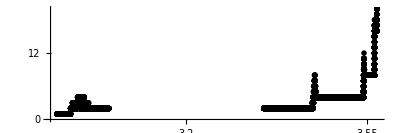

```mathematica
(*
	data=Flatten[ParallelTable[{μ,conf[μ,#⟦1⟧,#⟦2⟧]},{μ,#⟦3⟧,#⟦4⟧,10^(-#⟦5⟧)}]&/@{{2,300,2.95,3.05,5},{4,600,3.35,3.5,5},{5,1000,3.5,3.57,6},{6,5000,3.564,3.57,6},{7,10000,3.568,3.5702,7}},1];
alternativamente
 data=ParallelTable[{μ,conf[μ,7,10000]},{μ,2.95,3.57,10^-7}] ma i tempi sono eccessivamente lunghi se vogliamo una precisione di 10^-7, per altro necessaria per gli ultimi μ ma non per i primi
*)
data=Import["https://raw.githubusercontent.com/ZinRicky/cammelli-tonanti/master/01_Esame/03_Dati/D_deviazioni2.csv"];
ListPlot[data,PlotRange->{All,{0,20}},AspectRatio->1/3,Ticks->{Range[2.5,4,0.05],Range[0,30,2]},ImageSize->Full]
```

Aiuto! Qui non ricalcola giusto data, perché tutti i punti hanno periodo al più 2 — e certamente il problema è dalla mia parte.

costruiamo una funzione che elimina i punti isolati e definiamo l’intervallo sospetto n-esimo come un intorno circolare del punto dove smettono di esserci 2^n punti. Scelto un dato step nel punto successivo, un intorno di 2·10^3 step dovrebbe essere sufficiente

```mathematica
polishlastdata[n_,error_,ddata_]:=First@Last@Cases[FixedPoint[
If[Last@Last@Cases[ddata,{_,2^n}]==Last@#⟦Length[Cases[ddata,{_,2^n}]]-error⟧&@Cases[ddata,{_,2^n}],ddata,Drop[ddata,-1]],ddata],{_,2^n}]
```

```mathematica
ricerca[n_,step_]:={polishlastdata[n,10,data]-10^3 step,polishlastdata[n,10,data]+10^3 step,step}
```

Passando alla ricerca minuta di μ_n: trovati gli intervalli sospetti si può facilmente vedere che avvicinandosi alla biforcazione la distanza tra la iterata N-esima e (N+2^n)-esima fa una “gobba” attorno ai punti di biforcazione.

il costo computazionale di cercare quella “gobba” non è poco, questo basta a giustificare la ricerca grossolana fatta precedentemente.

```mathematica
dist[μ_,x0_,Ν_,n_]:=Abs[fn[μ,x0,Ν]-fn[μ,x0,Ν+2^n]]
indagine[n_,x0_,Ν_,{min_,max_,step_}]:=ParallelTable[{μ,dist[μ,x0,Ν,n]},{μ,min,max,step}]
indaginePlot[n_,x0_,Ν_,{min_,max_,step_}]:=ListPlot[indagine[n,x0,Ν,{min,max,step}],AspectRatio->1,PlotRange->Full]
sospetto[n_,x0_,Ν_,{min_,max_,step_}]:=Module[
{
ind=indagine[n,x0,Ν,{min,max,step}],
val,
spike
},
val=Last/@ind;
spike=Max@val;
Cases[ind,{_,spike}]
]
colpevole[n_,x0_,Ν_,{min_,max_,step_}]:=sospetto[n,x0,Ν,{min,max,step}]⟦1,1⟧
```

Possiamo calcolare i μ_n cercando i punti di massimo nelle gobbe; l’errore relativo è minimo ed il calcolo è veloce.

```mathematica
μsusp[n_]:= colpevole[n+2,0.4,10^Max[{5,n+2}],ricerca[n,10^(-Max[{5,n+2}])]]
μs=μsusp[#]&/@Range[0,6]; (*questo passaggio serve a farglieli calcolare una volta sola e salvarli in una lista*)
feigenbaum =Table[(μs⟦n⟧-μs⟦n-1⟧)/(μs⟦n+1⟧-μs⟦n⟧),{n,2,6}]
```

$Aborted

Part::partd: Part specification μs⟦2⟧ is longer than depth of object.

Part::partd: Part specification μs⟦1⟧ is longer than depth of object.

Part::partd: Part specification μs⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{(-μs⟦1⟧+μs⟦2⟧)/(-μs⟦2⟧+μs⟦3⟧),(-μs⟦2⟧+μs⟦3⟧)/(-μs⟦3⟧+μs⟦4⟧),(-μs⟦3⟧+μs⟦4⟧)/(-μs⟦4⟧+μs⟦5⟧),(-μs⟦4⟧+μs⟦5⟧)/(-μs⟦5⟧+μs⟦6⟧),(-μs⟦5⟧+μs⟦6⟧)/(-μs⟦6⟧+μs⟦7⟧)}

possiamo concludere che la costante di Feigenbaum è molto vicina a

```mathematica
ϕ=GeometricMean[feigenbaum]
```

Un altro importante passo è cercare μ_∞ in quanto è il punto che segna la divisione tra il comportamento regolare e quello caotico della mappa. Il nostro metodo ci dà un’approssimazione decente assumendo una crescita geometrica; avremo un’ulteriore conferma (ed un valore più preciso) di μ_∞nella parte successiva;

sappiamo che ϕ=(μ_n-μ_(n-1))/(μ_(n+1)-μ_n) ⇒ ϕ(μ_(n+1) - μ_n) = μ_n- μ_(n-1) ⇒ μ_(n+1) =1/ϕ (ϕ+1) μ_n - μ_(n-1)

cercando una formula chiusa,

```mathematica
m[0]=μ0;
m[1]=μ1;
m[n_]:=( (ϕ+1)/ϕ)m[n-1]-m[n-2]/ϕ
m[3]//Simplify
m[4]//Simplify
m[5]//Simplify
```

(-μ0 (1+ϕ)+μ1 (1+ϕ+ϕ^2))/ϕ^2

(-μ0 (1+ϕ+ϕ^2)+μ1 (1+ϕ+ϕ^2+ϕ^3))/ϕ^3

(-μ0 (1+ϕ+ϕ^2+ϕ^3)+μ1 (1+ϕ+ϕ^2+ϕ^3+ϕ^4))/ϕ^4

è piuttosto chiaro che la formula chiusa che cerchiamo è μ_n= (-μ_0(1+...+ϕ^(n-2)) + μ_1(1+...+ϕ^(n-1)))/ϕ^(n-1)

```mathematica
μ[n_]:=(-3(∑_(i=0)^(n-2) ϕ^i)+(1+√6)(∑_(i=0)^(n-1) ϕ^i))/ϕ^(n-1)
μ[0]=3;
μ[20000]
```

dovrebbe essere un’ottima approssimazione di μ_∞.

ora che abbiamo una formula chiusa possiamo studiare i punti μ_n con più precisione; Alla biforcazione n, ogni punto fisso di f^(2^n) biforca producendo due punti fissi di f^(2^(n+1)); al crescere di μ, la distanza fra questi due punti fissi aumenta. possiamo studiare come variano i massimi di queste distanze.

questo si fa studiando le distanze tra i punti delle orbite nei μ di biforcazione

```mathematica
d[n_]:=Min[Abs[fn[μ[n],0.4,10^5]-fn[μ[n],0.4,10^5+#]&/@Range[2^n]]]
ListPlot[d[#+1]/d[#]&/@Range[5]]
d[20001]/d[20000]
```

La costante di Feigenbaum ϕ è universale, ossia la successione μ_n dipende dalla mappa su cui la si cerca solo nella misura in cui la mappa fornisce μ_0e μ_1, non ϕ. questa cosa si può vedere studiando nel medesimo modo una seconda mappa:

```mathematica
s[λ_,x_]:= λ Sin[π x]
sn=Compile[{{λ,_Real},{x,_Real},{n,_Integer}},Nest[s[λ,π #]&,x,n]];
attrattivoPlotSen[nx_,n_,{μ0_,μ1_,η_}]:=With[{f=Function[{μ,x},μ Sin[π x]]},
ListPlot[
Union@Flatten[Table[
ParallelTable[
{μ,FixedPoint[Chop[f[μ,#]]&,x0,n]},{μ,Subdivide[μ0,μ1,η]}],
{x0,Subdivide[0,1.,nx]}
],1],
PlotStyle->{AbsolutePointSize[0.015],Black},
PlotRange->{{μ0,μ1},{0,1}},AspectRatio->Automatic,
Ticks->{Subdivide[0,4.,20],Subdivide[0,1.,10]}
]
]
senPlot=attrattivoPlotSen[30,10^4,{0,1.5,10^4}]
```

la mappa presenta un comportamento simile a quello della logistica al variare di λ; cerchiamo λ_0e λ_1.

```mathematica
cons[λ_,n_,iterations_]:=Length[Union[Round[10^4(sn[λ,0.4,iterations+#]-sn[λ,0.4,iterations]),1]& /@Range[2^n]]]
dataSin=ParallelTable[{λ,cons[λ,3,10000]},{λ,0.65,0.9,10^-6}]
distS[λ_,x0_,Ν_,n_]:=Abs[sn[λ,x0,Ν]-sn[λ,x0,Ν+2^n]]
indagineS[n_,x0_,Ν_,{min_,max_,step_}]:=ParallelTable[{λ,distS[λ,x0,Ν,n]},{λ,min,max,step}]
indaginePlotSen[n_,x0_,Ν_,{min_,max_,step_}]:=ListPlot[indagineS[n,x0,Ν,{min,max,step}],AspectRatio->1,PlotRange->Full]
sospettoS[n_,x0_,Ν_,{min_,max_,step_}]:=Module[
{
ind=indagineS[n,x0,Ν,{min,max,step}],
val,
spike
},
val=Last/@ind;
spike=Max@val;
Cases[ind,{_,spike}]
]
colpevoleS[n_,x0_,Ν_,{min_,max_,step_}]:=sospettoS[n,x0,Ν,{min,max,step}]⟦1,1⟧
ricercaS[n_,step_]:={First@Last@Cases[dataSin,{_,2^n}]-10^3 step,First@Last@Cases[dataSin,{_,2^n}]+10^3 step,step}
λsosp[n_]:= colpevoleS[n+2,0.4,10^5,ricercaS[n,10^-Max[{5,n+2}]]]
```

stavolta lo useremo solo per trovare 2 valori e costruire di conseguenza la successione con la vecchia costante di Feigenbaum

```mathematica
λ0=λsosp[0]
λ1=λsosp[1]
λ[n_]:=(-λ0(∑_(i=0)^(n-2) ϕ^i)+λ1(∑_(i=0)^(n-1) ϕ^i))/ϕ^(n-1)
λ[0]:=λ0
```

Mostriamo che abbiamo ragione:

```mathematica
Show[{senPlot,Table[InfiniteLine[{{λ[n],0},{λ[n],1}}],{n,0,6}]}]
```